```mathematica
Lecture 13: Combinatorics
```

## Words

### Exercise Subsection

Let a[n] be the number of words of length n with letters 0 or 1 that feature at least 2 consecutive 0’s.  Create a list of the first 20 values for a[n], then look this sequence up in the OEIS (see https://oeis.org/ ).

```mathematica
a[n_]:=Count[Tuples[{0,1},n],{___,0,0,___}]
```

```mathematica
a/@Range@20
```

{0,1,3,8,19,43,94,201,423,880,1815,3719,7582,15397,31171,62952,126891,255379,513342,1030865}

```mathematica
Table[2^n-Fibonacci[n+2],{n,1,20}]
```

{0,1,3,8,19,43,94,201,423,880,1815,3719,7582,15397,31171,62952,126891,255379,513342,1030865}

### Exercise Subsection

a. How many words of length 6 with letters in 1,2,3,4,5,6 (that is, consider Tuples[Range@6,6]) never have i in position i for any i?

b. Use the Monte-Carlo method to estimate the probability that a random word of length n with letters in 1,2,...,n never has i in position i for any i.

```mathematica
Length@Select[Tuples[Range@6,6],Not@MemberQ[#-Range@6,0]&]/Length@Tuples[Range@6,6]//N
```

0.334898

```mathematica
test[w_]:=Not@MemberQ[w-Range@Length@w,0]
```

```mathematica
Count[Table[test@RandomInteger[{1,35},35],{i,1000000}],True]
```

362313

```mathematica
3486669/10^7//N
```

0.348667

### Exercise Subsection

What is the probability that a randomly selected Permutation of {1,2,2,3,3,3,4,4,4,4} begins with a 4?

### Exercise Subsection

How many ways can the letters in the word “knickknack” be permuted such that consecutive letters are never the same?

```mathematica
Length@Permutations@Characters@"knickknack"-Count[Permutations@Characters@"knickknack",{___,a_,b_,___}/;a==b]
```

4620

### Exercise Subsection

How many ways can 1,1,2,2,3,3,4,4,5,5 can be permuted such that i is never next to i for any i?

### Exercise Subsection

What is the probability that a random word of length 12 with letters 1,2,3,4 has its letters appearing in nondecreasing order?

```mathematica
Count[Table[#==Sort@#&@RandomInteger[{1,4},12],{i,10000000}],True]
```

282

```mathematica
282/10^7//N
```

0.0000282

### Exercise Subsection

Write a function called SameBirthdayProbability[n] which uses the Monte-Carlo method to estimate the probability that at least two numbers on a list of n random integers selected between 1 and 365 will be the same.  For which value of n is this probability 0.5?  0.75?  0.90?

## Permutations

### Exercise Subsection

If p is a permutation of 1,2,...,n, then the permutation matrix for p is the matrix with i,j entry equal to 1 if i is equal to p[[j]] and 0 otherwise.  It is implemented in Mathematica as PermutationMatrix[p] (Mathematica stores this matrix as a “structured array” for more efficient storage and calculations, it can be turned into the standard form of a matrix using “Normal”.)

a. Write a function named FromPermutationMatrix that is the inverse function to PermutationMatrix.

```mathematica
Normal@PermutationMatrix[{1,2,5,3,4}]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1},{0,0,1,0,0},{0,0,0,1,0}}

```mathematica
Total[Transpose[{{1,0,0,0,0},{0,1,0,0,0},{0,0,0,0,1},{0,0,1,0,0},{0,0,0,1,0}}]{1,2,3,4,5}]
```

{1,2,5,3,4}

```mathematica
FromPermutationMatrix[m_]:=Total[Transpose[m]Range[Length@m]]
```

```mathematica
FromPermutationMatrix@PermutationMatrix[{7,6,5,4,3,2,1}]
```

{7,6,5,4,3,2,1}

b. Write a function named OrderTwo[n_] that inputs an integer n and outputs the number of permutations of 1,2,...,n that have a PermutationMatrix that is symmetric. Create a list of the first 8 values of Derangements, then look this sequence up in the OEIS (see https://oeis.org/ ).

```mathematica
?SymmetricMatrixQ
```

```mathematica
Length@Select[Permutations@Range@5,SymmetricMatrixQ@*PermutationMatrix]
```

26

```mathematica
OrderTwo[n_]:=Length@Select[Permutations@Range@n,SymmetricMatrixQ@*PermutationMatrix]
```

```mathematica
OrderTwo/@Range@8
```

{1,2,4,10,26,76,232,764}

c. Use SeriesCoefficient to create a list of the coefficient of x^n in the series centered at x = 0 for the function Exp[x + x^2/2] as n ranges from 0 to 10.  Show that multiplying the coefficient of x^n by n! gives the same result as the solution to part c.

```mathematica
Table[SeriesCoefficient[Exp[x + x^2/2],{x,0,n}],{n,1,10}](Range@10)!
```

{1,2,4,10,26,76,232,764,2620,9496}

```mathematica
Series[Exp[x + x^2/2],{x,0,10}]
```

1+x+x^2+(2 x^3)/3+(5 x^4)/12+(13 x^5)/60+(19 x^6)/180+(29 x^7)/630+(191 x^8)/10080+(131 x^9)/18144+(1187 x^10)/453600+O[x]^11

### Exercise Subsection

A permutation of 1,2,...,n is alternating if there are never three consecutive integers in the permutation a,b,c with either a<b<c or c<b<a.  

a. Write a function named Alternating[n] that inputs an integer n and outputs the number of alternating permutations of n.  Create a list of the first 8 values of Alternating, then look this sequence up in the OEIS (see https://oeis.org/ ).

b. Use Table together with SeriesCoefficient to create a list of length 8 such with nth element equal to n! times the coefficient of x^n in the series centered at x = 0 for the function (Tan[x]+Sec[x])^2.  This table should give the same values as the function Alternating.

## Lattice Paths

### Exercise Subsection

a. The Motzkin sequence of lists is defined recursively in the next cell.

```mathematica
Motzkin[n_]:=Motzkin[n]=If[n==0,{{}},
Join[Prepend[#,0]&/@Motzkin[n-1],
Flatten[Table[Flatten@{1,a,-1,b},{i,0,n-2},{a,Motzkin[i]},{b,Motzkin[n-i-2]}],2]]]
```

Starting with the empty list, the function Motzkin[n] is all of the lists that can be created by

1. adding 0 to the front of every list in Motzkin[n-1], or
2. creating a list of the form {1, a, -1, b} where a is a list in Motzkin[i] and b is a list in Motzkin[n-i-2] for some i. 

The result is that Motzkin[n] gives all lists of 0’s, 1’s and -1’s of length n such that each partial sum is nonnegative. 

a. Map the function Accumulate (this gives the partial sums of a list) onto Motzkin[8] and then verify that all lists in Motzkin[8] have nonnegative partial sums.

```mathematica
Accumulate/@Motzkin[8]
```

```mathematica
RandomChoice[Motzkin[8]]
```

{0,1,-1,1,0,-1,0,0}

b. Define a function DrawPath[L_] which has input one of the lists L that is outputted by Motzkin[n] and does the following:

1. Replaces each 0 in L with {1,0}, each 1 in L with {1,1}, and each -1 in L with {1,-1}.
2. Uses Prepend to place {0,0} at the start of the list.
3. Uses Accumulate to find coordinates in the x,y plane found from the partial sums of the steps in the list.
4. Uses Graphics to draw the Line segments that pass through the coordinates.

The output of DrawPath should be a path in the plane that starts at {0,0}, ends at {n,0}, and never travels below the x-axis.

```mathematica
DrawPath[L_]:=Graphics[{Red,Line@Accumulate@Prepend[ReplaceAll[L,{0->{1,0},1->{1,1},-1->{1,-1}}],{0,0}]}]
```

c. Use DrawPath on a list in Motzkin[15] selected at random using RandomChoice.

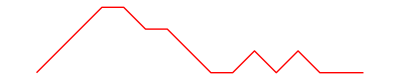

```mathematica
DrawPath@RandomChoice@Motzkin@15
```

## Generating functions

### Exercise Subsection

The generating function for the sequence a[n] is equal to Sum[a[n] x^n, {n,0,∞}].  Find the generating functions for each of the following sequences defined in this list:

```mathematica
Table[Binomial[n,5],{n,0,20}]
```

{0,0,0,0,0,1,6,21,56,126,252,462,792,1287,2002,3003,4368,6188,8568,11628,15504}

```mathematica
Sum[Binomial[n,5](x-4)^n,{n,0,Infinity}]
```

(-1024+1280 x-640 x^2+160 x^3-20 x^4+x^5)/(-5+x)^6

```mathematica
Series[(-1024+1280 x-640 x^2+160 x^3-20 x^4+x^5)/(-5+x)^6,{x,4,20}]
```

(x-4)^5+6 (x-4)^6+21 (x-4)^7+56 (x-4)^8+126 (x-4)^9+252 (x-4)^10+462 (x-4)^11+792 (x-4)^12+1287 (x-4)^13+2002 (x-4)^14+3003 (x-4)^15+4368 (x-4)^16+6188 (x-4)^17+8568 (x-4)^18+11628 (x-4)^19+15504 (x-4)^20+O[x-4]^21

```mathematica
sequences={Binomial[n,5],Binomial[5,n],Fibonacci[n],y^n/n!,Binomial[2n,n]};
```

```mathematica
Sum[sequences x^n,{n,0,Infinity}]
```

{x^5/(-1+x)^6,(1+x)^5,-x/(-1+x+x^2),ⅇ^(x y),1/(√(1-4 x))}

### Exercise Subsection

Let change[n] be the number of ways to make change for n cents using pennies, nickels, dimes, quarters, and dollar coins.  The generating function for change[n] is in the next cell.  Use Series and Coefficient to find the number of ways to make change for 100 cents.

```mathematica
Series[1/Product[(1-x^i),{i,{1,5,10,25,100}}],{x,0,100}]
```

1+x+x^2+x^3+x^4+2 x^5+2 x^6+2 x^7+2 x^8+2 x^9+4 x^10+4 x^11+4 x^12+4 x^13+4 x^14+6 x^15+6 x^16+6 x^17+6 x^18+6 x^19+9 x^20+9 x^21+9 x^22+9 x^23+9 x^24+13 x^25+13 x^26+13 x^27+13 x^28+13 x^29+18 x^30+18 x^31+18 x^32+18 x^33+18 x^34+24 x^35+24 x^36+24 x^37+24 x^38+24 x^39+31 x^40+31 x^41+31 x^42+31 x^43+31 x^44+39 x^45+39 x^46+39 x^47+39 x^48+39 x^49+49 x^50+49 x^51+49 x^52+49 x^53+49 x^54+60 x^55+60 x^56+60 x^57+60 x^58+60 x^59+73 x^60+73 x^61+73 x^62+73 x^63+73 x^64+87 x^65+87 x^66+87 x^67+87 x^68+87 x^69+103 x^70+103 x^71+103 x^72+103 x^73+103 x^74+121 x^75+121 x^76+121 x^77+121 x^78+121 x^79+141 x^80+141 x^81+141 x^82+141 x^83+141 x^84+163 x^85+163 x^86+163 x^87+163 x^88+163 x^89+187 x^90+187 x^91+187 x^92+187 x^93+187 x^94+213 x^95+213 x^96+213 x^97+213 x^98+213 x^99+243 x^100+O[x]^101

### Exercise Subsection

The generating function for the Legendre polynomial is in the next cell.  Use Series and Coefficient to find the 10th Legendre polynomial.

```mathematica
Coefficient[Series[1/(√(1-2 t x+x^2)),{x,0,10}],x^10]//Expand
```

-63/256+(3465 t^2)/256-(15015 t^4)/128+(45045 t^6)/128-(109395 t^8)/256+(46189 t^10)/256